# Числено интегриране. Квадратурни формули на Нютон-Коутс

## Използване на вградените възможности на Wolfram

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
∫_3^4 f[x]ⅆx
```

1/2 √(3 π) (Erfi[4/(√3)]-Erfi[√3])

```mathematica
%//N
```

76.1938

```mathematica
f[x_]:=((ⅇ^(x^2))^(1/3))/Sin[x]
∫_3^4 f[x]ⅆx
```

Integrate::idiv: Integral of ⅇ^(x^2/3) Csc[x] does not converge on {3,4}.

∫_3^4 (ⅇ^(x^2))^(1/3) Csc[x]ⅆx

```mathematica
∫_3^4 f[x]ⅆx//N
```

Integrate::idiv: Integral of ⅇ^(x^2/3) Csc[x] does not converge on {3,4}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.14256}. NIntegrate obtained -988.095 and 843.283 for the integral and error estimates.

-988.095

## Съставяне на мрежата

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
h = 0.1;
n = (b-a)/h;
xt = Table[a+i*h, {i,0,n}]
```

{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
yt = f[xt]
```

{20.0855,24.6144,30.3663,37.7128,47.15,59.343,75.1886,95.9026,123.141,159.174,207.127}

## Леви правоъгълници

```mathematica
I1 = h*∑_(i=0)^(n-1) f[a+i*h]
```

67.2679

за сравнение:

```mathematica
Itochno
```

76.1938

#### Оценка на грешката

намиране на M1

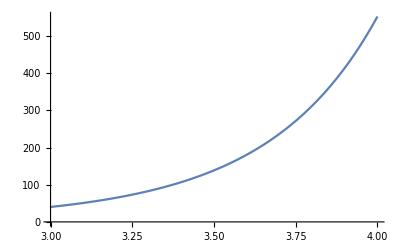

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

```mathematica
M1 = Abs[f'[b]]
```

(8 ⅇ^(16/3))/3

```mathematica
%//N
```

552.339

```mathematica
R1 = (b-a)^2/(2n)*M1
```

27.617

Истинска грешка

```mathematica
Abs[I1-Itochno]
```

8.92594

### Всичко на едно място

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
h = 0.1;
n = (b-a)/h;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[b]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на левите правоъгълници е ", I1]
Print["Точната стойност е                                        ", Itochno]
Print["Теоретичната грешка по метода на левите правоъгълници е ", R1]
Print["Истинската грешка е                                     ", Abs[I1-Itochno]]
```

Мрежата е със стъпка h = 0.1 и брой подинтервали n = 10.

Приблежената стойност по метода на левите правоъгълници е 67.2679

Точната стойност е                                        76.1938

Теоретичната грешка по метода на левите правоъгълници е 27.617

Истинската грешка е                                     8.92594

## Десни правоъгълници

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
h = 0.1;
n = (b-a)/h;
I2 = h*∑_(i=1)^n f[a+i*h];
M1 = Abs[f'[b]];
R2 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на десните правоъгълници е ", I2]
Print["Точната стойност е                                        ", Itochno]
Print["Теоретичната грешка по метода на десните правоъгълници е ", R2]
Print["Истинската грешка е                                     ", Abs[I2-Itochno]]
```

Мрежата е със стъпка h = 0.1 и брой подинтервали n = 10.

Приблежената стойност по метода на десните правоъгълници е 85.9721

Точната стойност е                                        76.1938

Теоретичната грешка по метода на десните правоъгълници е 27.617

Истинската грешка е                                     9.77823

## Средни правоъгълници

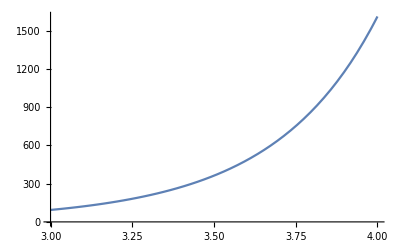

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
h = 0.1;
n = (b-a)/h;
I3 = h*∑_(i=0)^(n-1) f[a+i*h+h/2];
M2 = Abs[f''[b]];
R3 = (b-a)^3/(24 n^2)*M2;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на средните правоъгълници е ", I3]
Print["Точната стойност е                                        ", Itochno]
Print["Теоретичната грешка по метода на средните правоъгълници е ", R3]
Print["Истинската грешка е                                     ", Abs[I3-Itochno]]
```

Мрежата е със стъпка h = 0.1 и брой подинтервали n = 10.

Приблежената стойност по метода на средните правоъгълници е 75.981

Точната стойност е                                        76.1938

Теоретичната грешка по метода на средните правоъгълници е 0.671246

Истинската грешка е                                     0.212823

## Трапеци - САМОСТОЯТЕЛНО

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

-Graphics-

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
h = 0.1;
n = (b-a)/h;
I3 = h*∑_(i=0)^(n-1) f[a+i*h+h/2];
M2 = Abs[f''[b]];
R3 = (b-a)^3/(24 n^2)*M2;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на средните правоъгълници е ", I3]
Print["Точната стойност е                                        ", Itochno]
Print["Теоретичната грешка по метода на средните правоъгълници е ", R3]
Print["Истинската грешка е                                     ", Abs[I3-Itochno]]
```

Мрежата е със стъпка h = 0.1 и брой подинтервали n = 10.

Приблежената стойност по метода на средните правоъгълници е 75.981

Точната стойност е                                        76.1938

Теоретичната грешка по метода на средните правоъгълници е 0.671246

Истинската грешка е                                     0.212823

## Симпсън

Условие за приложение - ако n (броят на подинтервалите) e четно число!

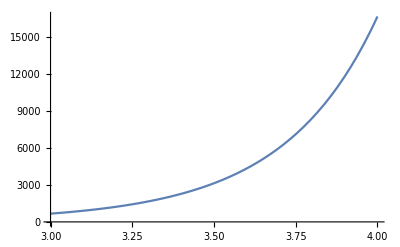

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
h = 0.1;
n = (b-a)/h; m = n/2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[b]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на Симпсън е ", IS]
Print["Точната стойност е                           ", Itochno]
Print["Теоретичната грешка по метода на Симпсън е ", RS]
Print["Истинската грешка е                        ", Abs[IS-Itochno]]
```

Мрежата е със стъпка h = 0.1 и брой подинтервали n = 10.

Приблежената стойност по метода на Симпсън е 76.1965

Точната стойност е                           76.1938

Теоретичната грешка по метода на Симпсън е 0.00924543

Истинската грешка е                        0.0026255

## Пресмятане с предварително зададена точност

```mathematica
eps = 10^-6;
```

```mathematica
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=eps, n]//N
```

n<0.||n≥2.7617×10^8

## Леви правоъгълници

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
n = 2.77*10^8;
h = (b-a)/n;
I1 = h*∑_(i=0)^(n-1) f[a+i*h]//N;
M1 = Abs[f'[b]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на левите правоъгълници е ", I1]
Print["Точната стойност е                                        ", Itochno]
Print["Теоретичната грешка по метода на левите правоъгълници е ", R1]
Print["Истинската грешка е                                     ", Abs[I1-Itochno]]
```

Мрежата е със стъпка h = 3.61011×10^-9 и брой подинтервали n = 2.77×10^8

Приблежената стойност по метода на левите правоъгълници е 76.1938

Точната стойност е                                        76.1938

Теоретичната грешка по метода на левите правоъгълници е 9.97002×10^-7

Истинската грешка е                                     3.3762×10^-7

## Десни правоъгълници - САМОСТОЯТЕЛНО

## Средни правоъгълници - САМОСТОЯТЕЛНО

## Трапци - САМОСТОЯТЕЛНО

## Симпсън

Условие за приложение - ако n (броят на подинтервалите) e четно число!

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

-Graphics-

```mathematica
M4 = Abs[f''''[b]]
```

(6508 ⅇ^(16/3))/81

```mathematica
eps = 10^-6;
Clear[n]
Reduce[(b-a)^5/(180 n^4)*M4<=eps, n]//N
```

n≤-98.0577||n≥98.0577

```mathematica
f[x_]:=(ⅇ^(x^2))^(1/3)
Itochno = ∫_3^4 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 3;b = 4;
n = 100;
h = (b-a)/n;
m = n/2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b])//N;
M4 = Abs[f''''[b]];
RS = (b-a)^5/(180 n^4)*M4//N;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на Симпсън е ", IS]
Print["Точната стойност е                           ", Itochno]
Print["Теоретичната грешка по метода на Симпсън е ", RS]
Print["Истинската грешка е                        ", Abs[IS-Itochno]]
```

Мрежата е със стъпка h = 1/100 и брой подинтервали n = 100

Приблежената стойност по метода на Симпсън е 76.1938

Точната стойност е                           76.1938

Теоретичната грешка по метода на Симпсън е 9.24543×10^-7

Истинската грешка е                        2.66152×10^-7